# Lista 03 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

Ao preparar o Notebook da lista, faça uso abundante de comentários e textos explicativos. Não se esqueça de rotular devidamente os eixos dos gráficos que produzir.

## 1.

Duas massas são conectadas a molas idênticas conforme o esquema mostrado na figura abaixo.

-Graphics-
As massas movem-se horizontalmente, sem atrito, e podem ter valores diferentes m_1 e m_2.
• Escreva as equações diferenciais para x_1(t) e x_2(t) que governam os movimentos das massas, em uma  forma que dependa apenas das quantidades ω_1^2 = k/m_1 e ω_2^2 = k/m_2 .

Para a um sistema de duas massas diferentes e molas iguais, temos a seguinte parametrização do sistema:  {m_1 x_1^(..)(t) = - ω_1^2(2x_1(t) - x_2(t))
m_1 x_2^(..)(t) = - ω_2^2(-x_1(t) + x_2(t)), onde a solução de x_1(t) e x_2(t) é extensa e complexa. No entanto, quando aplicamos as condições iniciais chegamos em uma expressão mais concisa. Para obtermos a solução das nossas edos, utilizaremos a função DSolve junto com FullSImplify, para obtermos uma solução analítica simplificada da descrição das posições.

```mathematica
eq1 ={x1''[t] + w1^2(2*x1[t] -x2[t]) == 0, x2''[t] + w2^2(-x1[t]+x2[t])== 0};
sol1a =DSolve[{eq1},{x1[t],x2[t]},t]//FullSimplify
```

{{x1[t]→(ⅇ^(-(t (√(-2 w1^2-w2^2-√(4 w1^4+w2^4))+√(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) (ⅇ^((t (2 √(-2 w1^2-w2^2-√(4 w1^4+w2^4))+√(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4)) ((-w2^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) C[1]+√2 C[2])+2 w1^2 (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) (C[1]-C[3])+√2 (C[2]-C[4])))+ⅇ^((t √(-2 w1^2-w2^2-√(4 w1^4+w2^4)))/(√2)) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) ((w2^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) C[1]-√2 C[2])+2 w1^2 (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) (-C[1]+C[3])+√2 (C[2]-C[4])))+ⅇ^((t √(-2 w1^2-w2^2+√(4 w1^4+w2^4)))/(√2)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4)) ((-w2^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) C[1]-√2 C[2])+2 w1^2 (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) (C[1]-C[3])+√2 (-C[2]+C[4])))+ⅇ^((t (√(-2 w1^2-w2^2-√(4 w1^4+w2^4))+2 √(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) ((w2^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) C[1]+√2 C[2])+2 w1^2 (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) (-C[1]+C[3])+√2 (-C[2]+C[4])))))/(4 √(4 w1^4+w2^4) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4))),x2[t]→(ⅇ^(-(t (√(-2 w1^2-w2^2-√(4 w1^4+w2^4))+√(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) (ⅇ^((t √(-2 w1^2-w2^2+√(4 w1^4+w2^4)))/(√2)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4)) (w2^2 (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) (-2 C[1]+C[3])+√2 (2 C[2]-C[4]))+(-2 w1^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) C[3]-√2 C[4]))+ⅇ^((t (√(-2 w1^2-w2^2-√(4 w1^4+w2^4))+2 √(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) (w2^2 (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) (2 C[1]-C[3])+√2 (2 C[2]-C[4]))+(2 w1^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) C[3]+√2 C[4]))+ⅇ^((t √(-2 w1^2-w2^2-√(4 w1^4+w2^4)))/(√2)) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) ((2 w1^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) C[3]-√2 C[4])+w2^2 (√(-2 w1^2-w2^2+√(4 w1^4+w2^4)) (2 C[1]-C[3])+√2 (-2 C[2]+C[4])))+ⅇ^((t (2 √(-2 w1^2-w2^2-√(4 w1^4+w2^4))+√(-2 w1^2-w2^2+√(4 w1^4+w2^4))))/(√2)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4)) ((-2 w1^2+√(4 w1^4+w2^4)) (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) C[3]+√2 C[4])+w2^2 (√(-2 w1^2-w2^2-√(4 w1^4+w2^4)) (-2 C[1]+C[3])+√2 (-2 C[2]+C[4])))))/(4 √(4 w1^4+w2^4) √(-2 w1^2-w2^2-√(4 w1^4+w2^4)) √(-2 w1^2-w2^2+√(4 w1^4+w2^4)))}}

• Determine a solução das equações de movimento quando ambas as massas partem do repouso, com m_1 inicialmente no equilíbrio e m_2com um deslocamento A.

Um corpo partir do repouso significa que não existia uma força agindo sobre ele, com isso, a velocidade do corpo será constante. Com isso, podemos escolher um referencial inercial de maneira que a velocidade inicial das massas são nulas, ou seja, x1’[0]== x2’[0]==0. Com as condições iniciais definidas podemos encorporá-las na função DSolve e utilizando FullSimplify teremos nossas soluções como uma sobreposição de funções trigonométricas hiperbólicas.

```mathematica
ci1 = {x1[0]== 0, x2[0]== A,x1'[0]==0,x2'[0]==0};
sol1b =DSolve[{eq1,ci1},{x1[t],x2[t]},t]//FullSimplify
```

{{x1[t]→(A w1^2 (-Cosh[(t √(-2 w1^2-w2^2-√(4 w1^4+w2^4)))/(√2)]+Cosh[(t √(-2 w1^2-w2^2+√(4 w1^4+w2^4)))/(√2)]))/(√(4 w1^4+w2^4)),x2[t]→(A ((-2 w1^2+w2^2+√(4 w1^4+w2^4)) Cosh[(t √(-2 w1^2-w2^2-√(4 w1^4+w2^4)))/(√2)]+(2 w1^2-w2^2+√(4 w1^4+w2^4)) Cosh[(t √(-2 w1^2-w2^2+√(4 w1^4+w2^4)))/(√2)]))/(2 √(4 w1^4+w2^4))}}

• Medindo distâncias em unidades de A e escolhendo valores para as frequências, trace, no mesmo conjunto de eixos, gráficos de x_1(t) e x_2(t), em um intervalo de tempo que compreenda várias oscilações, para os casos:
		(i)  ω_1 = ω_2
		(ii)  ω_1 ≪ ω_2
		(iii)  ω_1 ≫ ω_2 
Interprete fisicamente os resultados.

Nesta etapa do exercício usaremos, para fins de simplificação  A = 1, pois por ele ser apenas uma constante multiplicando nossas soluções e o enunciado pede para medir a distância em unidades de A, que seria a mesma coisa que dividir a função por A, tender A à 1, tem o mesmo efeito. Dito isso, plotamos abaixo cada caso citado no enunciado.

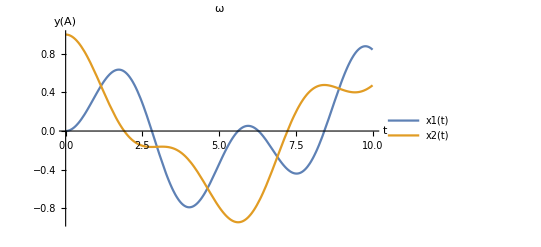

```mathematica
parametrosi = {A -> 1,w1-> 1,w2-> 1 };
x1i= sol1b[[1,1]]/.parametrosi;
x2i= sol1b[[1,2]]/.parametrosi;
Plot[{x1[t]/.x1i,x2[t]/.x2i}, {t,0,10}, AxesLabel->{"t","y(A)"}, PlotLegends->{"x1(t)","x2(t)"}, PlotLabel->"ω"]
```

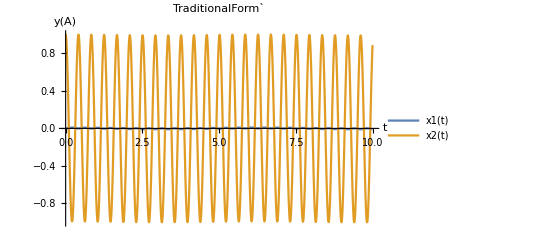

```mathematica
parametrosii = {A -> 1, w1-> 1,w2-> 15};
x1ii= sol1b[[1,1]]/.parametrosii;
x2ii= sol1b[[1,2]]/.parametrosii;
Plot[{x1[t]/.x1ii,x2[t]/.x2ii}, {t,0,10},PlotPoints->100, AxesLabel->{"t","y(A)"}, PlotLegends->{"x1(t)","x2(t)"}, PlotLabel->"TraditionalForm`"]
```

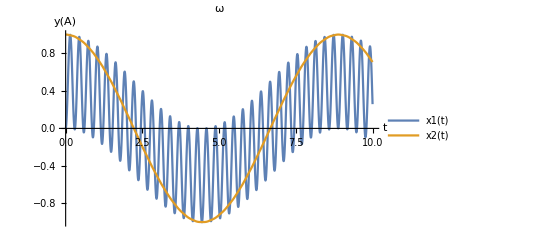

```mathematica
parametrosiii = {A -> 1, w1->15,w2-> 1};
x1iii= sol1b[[1,1]]/.parametrosiii;
x2iii= sol1b[[1,2]]/.parametrosiii;
Plot[{x1[t]/.x1iii,x2[t]/.x2iii}, {t,0,10},PlotPoints->100, AxesLabel->{"t","y(A)"}, PlotLegends->{"x1(t)","x2(t)"}, PlotLabel->"ω"]
```

• Fixando A = 1, ω_1 = 1 e ω_2= 1, determine os quatro primeiros instantes em que x_1(t) = x_2(t), de modo que não há instantaneamente energia armazenada na mola da direita.

Para encontra as raízes da função, utilizei o cursor do Mathematica sobre o primeiro caso plotado,  obtendo as quatro primeiras coordenadas de x  onde x_1 e x_2 se intersectam.

```mathematica
x11[t_] := x1[t]/.x1i
x22[t_] := x2[t]/.x2i
instante1 =FindRoot[x11[t]== x22[t],{t,1.09}]
instante2 =FindRoot[x11[t]== x22[t],{t,2.94}]
instante3 =FindRoot[x11[t]== x22[t],{t,4.60}]
instante4 =FindRoot[x11[t]== x22[t],{t,6.82}]
```

{t→1.15211}

{t→2.975}

{t→4.62207}

{t→6.89855}

## 2.

A tensão superficial σ da água em contato com o ar foi medida experimentalmente em várias temperaturas, produzindo os dados constantes da tabela abaixo.
-Graphics-
• Espera-se que a dependência de σ com a temperatura T seja linear, satisfazendo σ = a + bT, sendo 𝒶 e 𝒷 constantes. Por meio de um ajuste de mínimos quadrados dos dados da tabela, determine 𝒶 e 𝒷, indicando suas unidades.

O primeiro passo será transformar os dados da tabela em uma lista de pares ordenados. Após isso, utilizaremos a função ListPlot para plotar os pontos descritos na lista de pares ordenados.

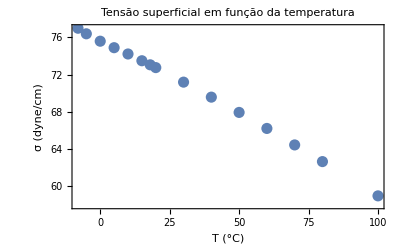

```mathematica
temp= {-8,-5,0,5,10,15,18,20,30,40,50,60,70,80,100};
sigma = {77.0,76.4,75.6,74.9,74.22,73.49,73.05,72.75,71.18,69.56,67.91,66.18,64.4,62.6,58.9};
sigmat= Transpose[{temp,sigma}];
graficodosponto = ListPlot[sigmat,PlotStyle->PointSize[0.02],FrameLabel->{"T (°C)","σ (dyne/cm)"}, Axes->False, Frame->True, PlotLabel->"Tensão superficial em função da temperatura"]
```

Para ajustar uma função no gráfico acima, utilizaremos a função Fit para ajustar um polinômio de primeiro grau junto com a função Chop, que considero nulo os coeficiente de ordem 10^-17. Por fim, criaremos um gráfico com a função ajuste encontrada e juntaremos o ajuste com os dados por meio da função Show.

```mathematica
ajuste=Fit[sigmat,{1,T},T]//Chop
```

75.8655-0.164624 T

Resposta: Com isso, tenho que a = 75.8655 dyne/cm e b = -0.164624 dyne/(cm °C)

• Faça gráficos, no mesmo conjunto de eixos, mostrando σ em função da temperatura tanto para os dados experimentais quanto segundo o ajuste obtido anteriormente.

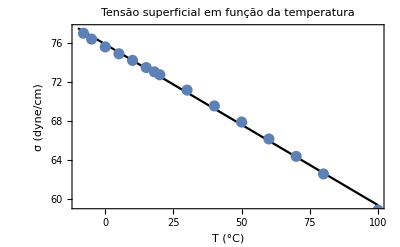

```mathematica
graficodoajuste = Plot[ajuste, {T,-10,100}, PlotStyle->Black];
Show[{graficodoajuste, graficodosponto},FrameLabel->{"T (°C)","σ (dyne/cm)"}, Axes->False, Frame->True, PlotLabel->"Tensão superficial em função da temperatura"]
```

## 3.

O movimento de uma partícula no plano 𝓍 e 𝓎 sob ação de uma força central atrativa de intensidade 𝒻 ∝ 1/ r^β é governado pela equação diferencial: m ⅆ^2/(ⅆ t^2)r⃗ = -(k r̂)/r^β, em que 𝓂 é a massa da partícula, 𝓀 é uma constante e r̂ = r⃗/r é um vetor unitário na direção do vetor posição r⃗ da partícula em relação ao centro de forças. (No caso de planetas orbitando o Sol), este é o centro de forças e temos β = 2.) A equação vetorial acima é equivalente às duas equações escalares acopladas: 
 m ⅆ^2/(ⅆ t^2)x = -(k x)/((√(x^2 + y^2))^(1 + β)) e m ⅆ^2/(ⅆ t^2)y = -(k y)/((√(x^2 + y^2))^(1 + β))
 Adote como condições iniciais do movimento x(0) = a, y(0) =0, x^• (0) = 0 e y^• (0) = 𝓋_0, de modo que não haja componente radial da velocidade inicial.  Para a solução numérica, escolha os valores positivos que preferir para 𝓂, 𝓀 e 𝒶.

• Analise primeiro o caso β = 2, escolhendo, com seus conhecimentos de Física I ou do Ensino Médio, o valor para 𝓋_0 que fornece uma trajetória circular. Resolva numericamente o sistema de equações diferenciais por pelo menos 4 períodos do movimento, utilizando a função ParametricPlot para se certificar de que a órbita obtida é de fato circular. Faça gráficos também tanto aumentando quanto diminuindo o valor da velocidade em relação ao primeiro caso, verificando que as novas órbitas obtidas são elípticas (fechadas).

Abaixo teremos a definição das funções e condições iniciais utilizadas ao longo do exercício, com uma ressalva de que para uma partícula com trajetória circular, a velocidade inicial deve ser dada pela seguinte expressão: y'[0]=√((k*A)/((√(x[0]^2 + y[0]^2))^2)). Além disso, consideramos A como sendo o período do movimento.

```mathematica
eqx3 = x''[t] == -((k/m)* x[t])/Sqrt[x[t]^2 + y[t]^2]^(1+β);
eqy3 = y''[t] == -((k/m)* y[t])/Sqrt[x[t]^2 + y[t]^2]^(1+β);
ci3 = { x[0] ==  A, x'[0] ==  0, y[0] ==  0, y'[0] ==  Sqrt[k*A/Sqrt[x[0]^2 + y[0]^2]^2]};
```

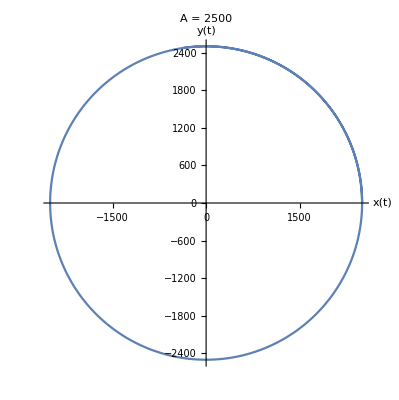

```mathematica
parametros31 = {m-> 1, k ->  10000, A -> 2500, β -> 2};
sol3a1 = NDSolve[{eqx3,eqy3,ci3}/.parametros31,{x,y},{t,10000}];
periodo1 =ParametricPlot[Evaluate[{x[t],y[t]}/.sol3a1],{t,0,10000}, AxesLabel->{"x(t)","y(t)"}, PlotLabel->"A = 2500"]
```

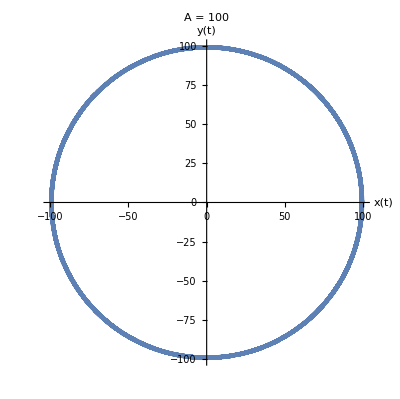

```mathematica
parametros32 = {m-> 1, k ->  10000, A -> 100, β -> 2};
sol3a2 = NDSolve[{eqx3,eqy3,ci3}/.parametros32,{x,y},{t,10000}];
periodo2 =ParametricPlot[Evaluate[{x[t],y[t]}/.sol3a2],{t,0,10000}, AxesLabel->{"x(t)","y(t)"}, PlotLabel->"A = 100"]
```

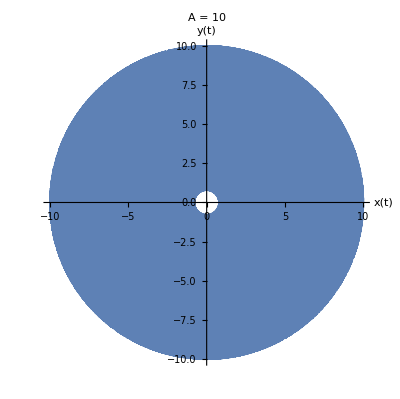

```mathematica
parametros33 = {m-> 1, k ->  10000, A -> 10, β -> 2};
sol3a3 = NDSolve[{eqx3,eqy3,ci3}/.parametros33,{x,y},{t,10000}];
periodo3 =ParametricPlot[Evaluate[{x[t],y[t]}/.sol3a3],{t,0,10000}, AxesLabel->{"x(t)","y(t)"}, PlotLabel->"A = 10"]
```

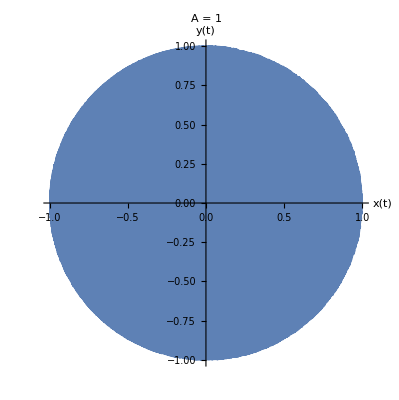

```mathematica
parametros34 = {m-> 1, k ->  10000, A -> 1, β -> 2};
sol3a4 = NDSolve[{eqx3,eqy3,ci3}/.parametros34,{x,y},{t,10000}];
periodo4 =ParametricPlot[Evaluate[{x[t],y[t]}/.sol3a4],{t,0,10000}, AxesLabel->{"x(t)","y(t)"}, PlotLabel->"A = 1"]
```